# Análisis cualitativo

## Espacio fase

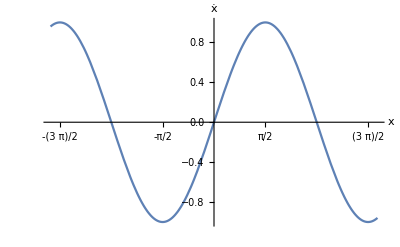

```mathematica
Plot[Sin[x],{x,-5,5},AxesLabel->{x,OverDot[x]},Ticks->{{-3*Pi/2,-Pi,-Pi/2,0,Pi/2,Pi,3*Pi/2},Automatic}]
```

## Soluciones exactas

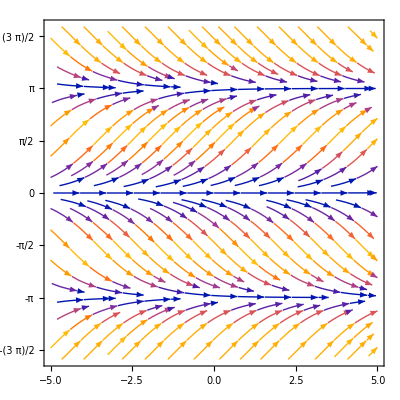

```mathematica
p1=StreamPlot[{1,Sin[x]},{t,-5,5},{x,-5,5},FrameTicks->{{{-3*Pi/2,-Pi,-Pi/2,0,Pi/2,Pi,3*Pi/2},None},{Automatic,None}}]
```

```mathematica
p2=ContourPlot[t+Log[Abs[Csc[x]+Cot[x]]],{t,-5,5},{x,-5,5},PlotPoints->100,FrameTicks->{{{-3*Pi/2,-Pi,-Pi/2,0,Pi/2,Pi,3*Pi/2},None},{Automatic,None}}]
```

-Graphics-